Numerical evoluation of p_(0,s) coefficients (without the overall factor of 2πω)

```mathematica
f[e_,s_]:=NIntegrate[Exp[I*s*(u-e*Sin[u])]/(1-e*Cos[u])^2, {u, 0, 2π}]
```

Analytical expression of p_(0,s) coefficients (without the overall factor of 2πω)

```mathematica
g[e_,s_]:=Integrate[Exp[I*s*(u-e*Sin[u])]/(1-e*Cos[u])^2, {u, 0, 2π},Assumptions->{Element[e,Reals], e>0}]
```

```mathematica
LogPlot[{f[e, 0],f[e,1], f[e, 2], f[e, 3]}, {e, 0, 1}, PlotLegends->{"p_(0, 0)","p_(0, 1)","p_(0, 2)","p_(0, 3)"},PlotLabel->Style["The first four p_(0, s) coefficients as a function of eccentricity",FontSize->32],AxesLabel->{Style["e",FontSize->24],Style["p_(0, s)",FontSize->24]}]
```

```mathematica
divergenceless[e_,s_]:=Integrate[Exp[I*s*(u-e*Sin[u])]*(1-e^2)^(3/2)/(1-e*Cos[u])^2, {u, 0, 2π},Assumptions->{Element[e,Reals], e>0,e<1}]
```

```mathematica
Series[g[e,1]*(1-e^2)^(3/2),{e,0,10}]
```

3 π e-(9 π e^3)/8+(9 π e^5)/64-(19 π e^7)/3072-(133 π e^9)/81920+O[e]^11

```mathematica
Column[Table[Print[Subscript[p, 0,s],":  " ,FullSimplify[Series[g[e,s]*(1-e^2)^(3/2),{e,0,10}]]], {s,0,10}]]
```

p_(0,0):  2 π

p_(0,1):  3 π e-(9 π e^3)/8+(9 π e^5)/64-(19 π e^7)/3072-(133 π e^9)/81920+O[e]^11

p_(0,2):  (9 π e^2)/2-(13 π e^4)/4+(27 π e^6)/32-(29 π e^8)/320+(67 π e^10)/11520+O[e]^11

p_(0,3):  (53 π e^3)/8-(879 π e^5)/128+(13893 π e^7)/5120-(21359 π e^9)/40960+O[e]^11

p_(0,4):  (77 π e^4)/8-(513 π e^6)/40+(2179 π e^8)/320-(19157 π e^10)/10080+O[e]^11

p_(0,5):  (1773 π e^5)/128-(68815 π e^7)/3072+(855815 π e^9)/57344+O[e]^11

p_(0,6):  (3167 π e^6)/160-(84003 π e^8)/2240+(538113 π e^10)/17920+O[e]^11

p_(0,7):  (432091 π e^7)/15360-(9987299 π e^9)/163840+O[e]^11

p_(0,8):  (178331 π e^8)/4480-(5863513 π e^10)/60480+O[e]^11

p_(0,9):  (64370707 π e^9)/1146880+O[e]^11

p_(0,10):  (7635529 π e^10)/96768+O[e]^11

```mathematica
Column[Table[Print[Subscript[p, 0,s],":  " ,FullSimplify[Series[g[e,s]*(1-e^2)^(3/2),{e,0,10+s}]]], {s,0,10}]]
```

p_(0,0):  2 π

p_(0,1):  3 π e-(9 π e^3)/8+(9 π e^5)/64-(19 π e^7)/3072-(133 π e^9)/81920-(14177 π e^11)/9830400+O[e]^12

p_(0,2):  (9 π e^2)/2-(13 π e^4)/4+(27 π e^6)/32-(29 π e^8)/320+(67 π e^10)/11520-(299 π e^12)/268800+O[e]^13

p_(0,3):  (53 π e^3)/8-(879 π e^5)/128+(13893 π e^7)/5120-(21359 π e^9)/40960+(41067 π e^11)/655360-(3547143 π e^13)/734003200+O[e]^14

p_(0,4):  (77 π e^4)/8-(513 π e^6)/40+(2179 π e^8)/320-(19157 π e^10)/10080+(71857 π e^12)/215040-(41663 π e^14)/1075200+O[e]^15

p_(0,5):  (1773 π e^5)/128-(68815 π e^7)/3072+(855815 π e^9)/57344-(30103445 π e^11)/5505024+(3055138525 π e^13)/2378170368-(438397391 π e^15)/2113929216+O[e]^16

p_(0,6):  (3167 π e^6)/160-(84003 π e^8)/2240+(538113 π e^10)/17920-(488317 π e^12)/35840+(5781747 π e^14)/1433600-(18910653 π e^16)/22528000+O[e]^17

p_(0,7):  (432091 π e^7)/15360-(9987299 π e^9)/163840+(671904569 π e^11)/11796480-(130846410289 π e^13)/4246732800+(83318824393 π e^15)/7549747200-(168738442158643 π e^17)/59793997824000+O[e]^18

p_(0,8):  (178331 π e^8)/4480-(5863513 π e^10)/60480+(83437241 π e^12)/806400-(576377581 π e^14)/8870400+(29950260751 π e^16)/1094860800-(31381640833 π e^18)/3773952000+O[e]^19

p_(0,9):  (64370707 π e^9)/1146880-(6955625097 π e^11)/45875200+(734132462571 π e^13)/4037017600-(8396796965937 π e^15)/64592281600+(845650572188427 π e^17)/13435194572800-(83532070070172513 π e^19)/3761854480384000+O[e]^20

p_(0,10):  (7635529 π e^10)/96768-(166026365 π e^12)/709632+(1767674785 π e^14)/5677056-(994626571585 π e^16)/3985293312+(363110363225 π e^18)/2656862208-(6130679273701 π e^20)/111588212736+O[e]^21

```mathematica
Column[Table[Print[Subscript[p, 0,s],":  " ,FullSimplify[Series[divergenceless[e,s],{e,1,10+s},Assumptions->e<1]]], {s,0,10}]]
```

p_(0,0):  2 π

p_(0,1):  Integrate[((1-e^2)^(3/2) ⅇ^(ⅈ (u-e Sin[u])))/(-1+e Cos[u])^2,{u,0,2 π},Assumptions→0<e<1]

$Aborted

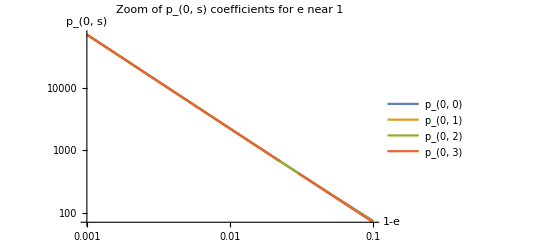

```mathematica
LogLogPlot[{f[1-x, 0],f[1-x,1],f[1-x,2],f[1-x,3]},{x,10^-3,10^-1},PlotPoints->100,PlotLegends->{"p_(0, 0)","p_(0, 1)","p_(0, 2)","p_(0, 3)"},PlotLabel->Style["Zoom of p_(0, s) coefficients for e near 1",FontSize->32],AxesLabel->{Style["1-e",FontSize->24],Style["p_(0, s)",FontSize->24]}]
```

```mathematica
The above look very linear, so check if the slope appears to be constant for e approaching 1
```

```mathematica
Limit[D[Log[g[1-Exp[-x],0]],x],x->Infinity]
```

3/2

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained 1.76692×10^-13-2.77556×10^-17 ⅈ and 1.36788×10^-12 for the integral and error estimates.

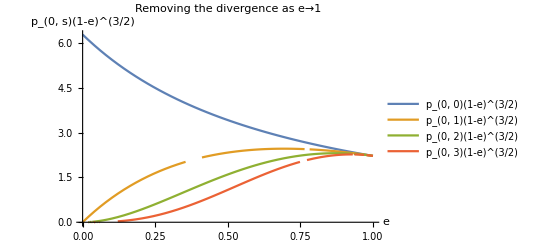

```mathematica
Plot[{f[e,0]*(1-e)^1.5,f[e,1]*(1-e)^1.5,f[e,2]*(1-e)^1.5,f[e,3]*(1-e)^1.5},{e,0,1},PlotLegends->{"p_(0, 0)(1-e)^(3/2)","p_(0, 1)(1-e)^(3/2)","p_(0, 2)(1-e)^(3/2)","p_(0, 3)(1-e)^(3/2)"},PlotLabel->Style["Removing the divergence as e→1",FontSize->32],AxesLabel->{Style["e",FontSize->24],Style["p_(0, s)(1-e)^(3/2)",FontSize->24]}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained 1.76692×10^-13-2.77556×10^-17 ⅈ and 1.36788×10^-12 for the integral and error estimates.

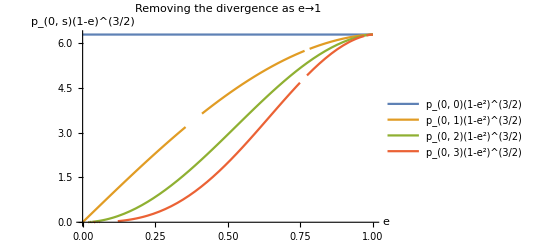

```mathematica
Plot[{f[e,0]*(1-e^2)^1.5,f[e,1]*(1-e^2)^1.5,f[e,2]*(1-e^2)^1.5,f[e,3]*(1-e^2)^1.5},{e,0,1},PlotLegends->{"p_(0, 0)(1-e^2)^(3/2)","p_(0, 1)(1-e^2)^(3/2)","p_(0, 2)(1-e^2)^(3/2)","p_(0, 3)(1-e^2)^(3/2)"},PlotLabel->Style["Removing the divergence as e→1",FontSize->32],AxesLabel->{Style["e",FontSize->24],Style["p_(0, s)(1-e)^(3/2)",FontSize->24]}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.2831853001364566677372607992192220043546624363983710281900130212}. NIntegrate obtained -6.33174×10^-16-2.23779×10^-16 ⅈ and 8.41455×10^-14 for the integral and error estimates.

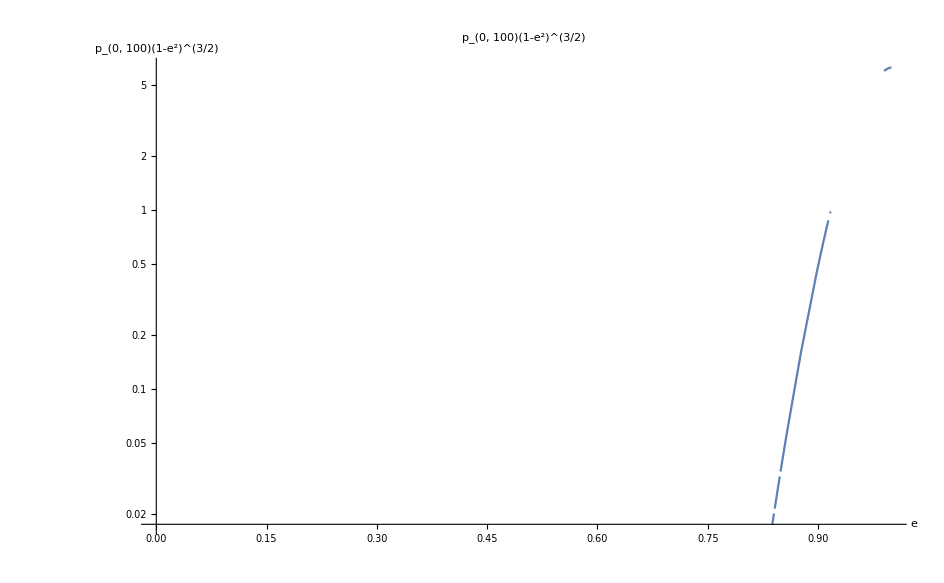

```mathematica
LogPlot[f[e,100]*(1-e^2)^1.5,{e,0,1},PlotLabel->Style["p_(0, 100)(1-e^2)^(3/2)",FontSize->32],AxesLabel->{Style["e",FontSize->24],Style["p_(0, 100)(1-e^2)^(3/2)",FontSize->24]}]
```

```mathematica
g[0.8,100]
```

```mathematica
Limit[g[1-x,0]*x^(3/2),x->0]
```

Indeterminate

```mathematica
Limit[f[e,0]*(1-e)^(3/2),e->1]
```

lim_(e→1) (1-e)^(3/2) f[e,0]

```mathematica
g[1-x,0]*x^(3/2)/.x->0.000001
```

2.22144+0. ⅈ

```mathematica
FullSimplify[Integrate[Cos[x]*Exp[-y]/(1-Cos[x]+Exp[-y]*Cos[x])^3, {x,0,2*π}]/Integrate[1/(1-Cos[x]+Exp[-y]*Cos[x])^2,{x,0,2*π}], Assumptions->{Element[y,Reals], y>0}]
```

(3 (-1+ⅇ^y))/(-2+4 ⅇ^y)

```mathematica
ArcSec[0.99]
```

0.+0.142014 ⅈ

```mathematica
Integrate[1/(1-y*Cos[x])^2,{x,0,2*π},Assumptions->{Element[y,Reals] && y>0 && y<1}]
```

(2 π)/((1-y^2)^(3/2))

```mathematica
g[y,0]
```

ConditionalExpression[(2 π)/((1-y^2)^(3/2)), y<1]

```mathematica
g[y,1]
```

Integrate[ⅇ^(ⅈ (u-y Sin[u]))/(1-y Cos[u])^2,{u,0,2 π},Assumptions→{y∈ℝ,y>0}]

```mathematica
2*π/2^1.5
```

2.22144